## Direct Derivation of the Dynamic Regressor for a Stanford Arm examples of the theoretical results presented in: "Explicit Lagrangian Formulation of the Dynamic Regressors for Serial Manipulators", M. Gabiccini, A. Bracci, D. De Carli, M. Fredianelli, A. Bicchi submitted to the 2009 IEEE International Conference on Robotics and Automation (ICRA2009) to be held in Kobe, Japan, May 12 - 17, 2009

### Package

```mathematica
<<ScrewCalculusPro`ScrewCalculusPro`
<<ToMatlab`ToMatlab`
```

### UR10e Manipulator - definition of required quantities

```mathematica
tableUR10e[q1_,q2_,q3_]={
{0,            -Pi/2,d1,q1,"R"},
{al2,           0        , d2, q2,"R"},
{al3,            0        ,d3,q3,"R"}}
```

{{0,-π/2,d1,q1,R},{al2,0,d2,q2,R},{al3,0,d3,q3,R}}

```mathematica
tableUR10e[q1_,q2_,q3_]={
{0,            -Pi/2, 0.1273,q1,"R"},
{0.6120,    0        , 0.220941,q2,"R"},
{0.5723,    0        ,-0.1719,q3,"R"}
}
```

{{0,-π/2,0.1273,q1,R},{0.612,0,0.220941,q2,R},{0.5723,0,-0.1719,q3,R}}

```mathematica
qsym={q1,q2,q3}
```

{q1,q2,q3}

```mathematica
CGtableUR10e ={{0,0,0},{a2,0,0},{a3,0,0}}
```

{{0,0,0},{a2,0,0},{a3,0,0}}

```mathematica
CGtableUR10e ={{0,0,0},
{-0.3060,0,0},
{-0.28615,0,0}}
```

{{0,0,0},{-0.306,0,0},{-0.28615,0,0}}

```mathematica
masslist=Table[ToExpression["m"<>ToString[i]],{i,1,Length[tableUR10e@@qsym]}]
```

{m1,m2,m3}

```mathematica
m1 =7.778;
m2 =12.93;
m3 = 3.87;
```

```mathematica
r=0.075;
h1=0.178;
h2=1.224;
h3=1.1446;
```

```mathematica
tensorlist ={
{{m1/12*(3*r^2+h1^2),0,0},{0,m1/2*(r^2),0},{0,0,m1/12*(3*r^2+h1^2)}},
{{m2/2*(r^2),0,0},{0,m2/12*(3*r^2+h2^2),0},{0,0,m2/12*(3*r^2+h2^2)}},
{{m3/2*(r^2),0,0},{0,m3/12*(3*r^2+h3^2),0},{0,0,m3/12*(3*r^2+h3^2)}}}
```

{{{1/12 m1 (h1^2+3 r^2),0,0},{0,(m1 r^2)/2,0},{0,0,1/12 m1 (h1^2+3 r^2)}},{{(m2 r^2)/2,0,0},{0,1/12 m2 (h2^2+3 r^2),0},{0,0,1/12 m2 (h2^2+3 r^2)}},{{(m3 r^2)/2,0,0},{0,1/12 m3 (h3^2+3 r^2),0},{0,0,1/12 m3 (h3^2+3 r^2)}}}

```mathematica
tensorlist ={{{0.031474312576900,0,0},{0,0.021875625000000,0},{0,0,0.031474312576900}},
{{0.036365625000000,0,0},{0,1.632467283798000,0},{0,0,1.632467283798000}},
{{0.010884375000000,0,0},{0,0.427952347172000,0},{0,0,0.427952347172000}}}
```

{{{0.0314743,0,0},{0,0.0218756,0},{0,0,0.0314743}},{{0.0363656,0,0},{0,1.63247,0},{0,0,1.63247}},{{0.0108844,0,0},{0,0.427952,0},{0,0,0.427952}}}

### Time dependent variable definitions [ALL REQUIRED]

Version time dependent, configuration

```mathematica
q[t_]=Map[ToExpression[ToString[#]<>"[t]"]&,qsym]
```

{q1[t],q2[t],q3[t]}

Velocity

```mathematica
qp[t_]=D[q[t],t]
```

{q1'[t],q2'[t],q3'[t]}

Acceleration

```mathematica
qpp[t_]=D[qp[t],t]
```

{q1''[t],q2''[t],q3''[t]}

Reference velocity in the Slotine-Li algorithm

```mathematica
v[t_]=Table[ToExpression["v"<>ToString[i]<>"[t]"],{i,1,Length[tableUR10e@@qsym]}]
```

{v1[t],v2[t],v3[t]}

Its time derivative

```mathematica
vp[t_]=D[v[t],t]
```

{v1'[t],v2'[t],v3'[t]}

Gravity is defined once as

```mathematica
g0={0,0,-g}
```

{0,0,-g}

### Direct regressor calculations

```mathematica
?Regressor
```

Dynamic Regressor for the first link alone

```mathematica
Y1=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,1]//FullSimplify);Y1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | v1'[t] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Y1//Dimensions
```

Dynamic Regressor for the second link alone

Regressor for the whole manipulator

```mathematica
Y=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0])
```

{1}
 |  |  |  |

```mathematica
Y//Dimensions
```

{3,30}

Structure of the Regressor for the Stanford Manipulator - the white columns show which parameters do not affect the manipulator dynamics

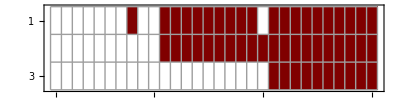

```mathematica
MatrixPlot[Y,ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All]
```

```mathematica
theFile=File["Y_r333333333.txt"];
Export[theFile,Y];
```

### Equations of motion obtained multiplying the Dynamic Regressor and the List of Dynamic Parameters

Contestualmente alla creazione della lista di parametri (10 per ciascun link) i momenti di inerzia vengono scritti rispetto all'origine del frame di DH ancora in componenti nel frame di DH.

As we create the complete list with masses, first moments of inertia and second moments of inertia, we calculate the moments of inertia with respect to the local D-H frames, as indicated in the paper

```mathematica
paramlist=ExtractParameters[CGtableUR10e,masslist,tensorlist]//Simplify;paramlist
```

{m1,0,0,0,1/12 m1 (h1^2+3 r^2),0,0,(m1 r^2)/2,0,1/12 m1 (h1^2+3 r^2),m2,a2 m2,0,0,(m2 r^2)/2,0,0,1/12 m2 (12 a2^2+h2^2+3 r^2),0,1/12 m2 (12 a2^2+h2^2+3 r^2),m3,a3 m3,0,0,(m3 r^2)/2,0,0,1/12 m3 (12 a3^2+h3^2+3 r^2),0,1/12 m3 (12 a3^2+h3^2+3 r^2)}

Extract just the parameters for the first link...

```mathematica
paramlist[[1;;10]]
```

Equations of motion with the regressor

```mathematica
regressoreqs=Y.paramlist;
```

### A little detour inside the package (just to show other useful functions)

```mathematica
FK= DHFKine[tableUR10e@@qsym]//FullSimplify
```

{{Cos[q1] Cos[q2+q3],-Cos[q1] Sin[q2+q3],-Sin[q1],Cos[q1] (al2 Cos[q2]+al3 Cos[q2+q3])-(d2+d3) Sin[q1]},{Cos[q2+q3] Sin[q1],-Sin[q1] Sin[q2+q3],Cos[q1],(d2+d3) Cos[q1]+(al2 Cos[q2]+al3 Cos[q2+q3]) Sin[q1]},{-Sin[q2+q3],-Cos[q2+q3],0,d1-al2 Sin[q2]-al3 Sin[q2+q3]},{0,0,0,1}}

```mathematica
theFile=File["FK_3r.txt"];
Export[theFile,FK];
```

```mathematica
JJ=DHJacob0[tableUR10e@@qsym]//FullSimplify
```

{{-(d2+d3) Cos[q1]-(al2 Cos[q2]+al3 Cos[q2+q3]) Sin[q1],-Cos[q1] (al2 Sin[q2]+al3 Sin[q2+q3]),-al3 Cos[q1] Sin[q2+q3]},{Cos[q1] (al2 Cos[q2]+al3 Cos[q2+q3])-(d2+d3) Sin[q1],-Sin[q1] (al2 Sin[q2]+al3 Sin[q2+q3]),-al3 Sin[q1] Sin[q2+q3]},{0,-al2 Cos[q2]-al3 Cos[q2+q3],-al3 Cos[q2+q3]},{0,-Sin[q1],-Sin[q1]},{0,Cos[q1],Cos[q1]},{1,0,0}}

```mathematica
theFile=File["J_3r.txt"];
Export[theFile,JJ];
```

Inertia matrix

```mathematica
Bmat[q1_,q2_,q3_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify
```

{{3.20474+2.12815 Cos[2 q2]+0.677729 Cos[q3]+0.366975 Cos[2 (q2+q3)]+0.677729 Cos[2 q2+q3],(0.990321+0.054308 Cos[q3]) Sin[q2]+0.054308 Cos[q2] Sin[q3],0.054308 Cos[q3] Sin[q2]+0.054308 Cos[q2] Sin[q3]},{(0.990321+0.054308 Cos[q3]) Sin[q2]+0.054308 Cos[q2] Sin[q3],5.0375+6.93889×10^-18 Cos[2 q1]-1.73472×10^-18 Cos[4 q1]+8.67362×10^-19 Cos[4 q1-2 q2]-3.46945×10^-18 Cos[2 (q1-q2)]-4.85723×10^-17 Cos[2 q2]-3.46945×10^-18 Cos[2 (q1+q2)]+8.67362×10^-19 Cos[2 (2 q1+q2)]-5.55112×10^-17 Cos[2 q2-q3]+1.35546 Cos[q3]+1.38778×10^-17 Cos[2 (q2+q3)]-5.55112×10^-17 Cos[2 q2+q3],0.744835+6.93889×10^-18 Cos[2 q1]-1.73472×10^-18 Cos[4 q1]+6.93889×10^-18 Cos[2 (q2-q3)]+3.46945×10^-18 Cos[4 q1+2 q2-q3]+0.677729 Cos[q3]+3.46945×10^-18 Cos[4 q1-2 q2+q3]+6.93889×10^-18 Cos[2 (q2+q3)]-2.77556×10^-17 Cos[2 q2+q3]},{0.054308 Cos[q3] Sin[q2]+0.054308 Cos[q2] Sin[q3],0.744835+6.93889×10^-18 Cos[2 q1]-1.73472×10^-18 Cos[4 q1]+6.93889×10^-18 Cos[2 (q2-q3)]+3.46945×10^-18 Cos[4 q1+2 q2-q3]+0.677729 Cos[q3]+3.46945×10^-18 Cos[4 q1-2 q2+q3]+6.93889×10^-18 Cos[2 (q2+q3)]-2.77556×10^-17 Cos[2 q2+q3],0.744835+1.38778×10^-17 Cos[q2]^2 Cos[2 q3]-1.38778×10^-17 Cos[q3]^2 Sin[q2]^2+Cos[q2] Cos[q3] (-5.55112×10^-17-2.77556×10^-17 Cos[q1]^2+2.77556×10^-17 Sin[q1]^2) Sin[q2] Sin[q3]+1.38778×10^-17 Sin[q2]^2 Sin[q3]^2}}

```mathematica
theFile=File["B_r3.txt"];
Export[theFile,Bmat[q1_,q2_,q3_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify];
```

```mathematica
Cmat=InertiaToCoriolis[Bmat@@q[t],q[t],qp[t]]//Simplify
```

```mathematica
theFile=File["C_r3.txt"];
Export[theFile,Cmat];
```

```mathematica
Gvec=Gravitational[tableUR10e@@qsym,CGtableUR10e,masslist,g0]//Simplify
```

{0,-g ((a2 m2+al2 (m2+m3)) Cos[q2]+(a3+al3) m3 Cos[q2+q3]),-(a3+al3) g m3 Cos[q2+q3]}

```mathematica
theFile=File["G_r3.txt"];
Export[theFile,Gvec];
```